The old and wrong equilibrium

```mathematica
psiw[s1_,s2_]:= (1/2 - (1/2)*(1 + 2 s1)/(1 + 2s2))
```

```mathematica
Simplify[psiw[s1,s2]]
```

(-s1+s2)/(1+2 s2)

```mathematica
betaw[t_,s2_,s1_]:= (s1 + psiw[s1, s2])/(1 + 2s1) + t/(1+2s2)
```

```mathematica
Simplify[betaw[t,s2,s1]]
```

(s2+t)/(1+2 s2)

```mathematica
line = Line[{{0.5,0},{0.5,1}}]
```

Line[{{0.5,0},{0.5,1}}]

```mathematica
Manipulate[Plot[{betaw[t1,s1,s2],betaw[t1,s2,s1]},{t1,0,1}, PlotRange->{0,1}, Frame->True, Epilog->{line}],{s1,0,1},{s2,0,1}]
```

```mathematica
betawinv[b_,s1_,s2_]:=t/. Solve[betaw[t,s1,s2]- b==0,t]
```

```mathematica
Simplify[betawinv[a,s1,s2]]
```

{a-s1+2 a s1}

```mathematica
betawinv[betaw[a,s2,s1],s1,s2]
```

{(a-s1+2 a s1+s2)/(1+2 s2)}

Asymmetric scenario with toeholds

```mathematica
psi[s1_,s2_] := ((s2 - s1)(1 + 2s1))/((1 + 2s1)(1 + s2) + s2(1 + s1))
```

```mathematica
Simplify[psi[s1,s2]]
```

-((1+2 s1) (s1-s2))/(1+2 s2+s1 (2+3 s2))

```mathematica
Simplify[t*(1 + 2s1)/(1 + 2s2) + psi[s1,s2]]
```

(1+2 s1) ((-s1+s2)/(1+2 s2+s1 (2+3 s2))+t/(1+2 s2))

```mathematica
beta[t_,s2_,s1_]:= (s1 + psi[s1, s2])/(1 + s1) + t/(1+2s2)
```

```mathematica
Simplify[beta[t,s2,s1]]
```

(s2+3 s1 s2)/(1+2 s1+2 s2+3 s1 s2)+t/(1+2 s2)

```mathematica
Manipulate[Plot[{beta[t1,s1,s2],beta[t1,s2,s1]},{t1,0,1}, PlotRange->{0,1}, Frame->True, Epilog->{line}],{s1,0,1},{s2,0,1}]
```

```mathematica
betainv[b_,s1_,s2_]:=t/. Solve[beta[t,s1,s2]- b==0,t]
```

```mathematica
Simplify[betainv[beta[a,s2,s1],s1,s2]]
```

{((1+2 s1) (a+2 a s2-(s1-s2) (1+2 s2)+a s1 (2+3 s2)))/((1+2 s2) (1+2 s2+s1 (2+3 s2)))}

```mathematica
Simplify[D[beta[t,s2,s1],s1]]
```

(s2 (1+3 s2))/(1+2 s2+s1 (2+3 s2))^2

```mathematica
Simplify[((1 + s1)*(s2 + psi[s2,s1])/(1 + s2)) -s1 + s1*(psi[s2,s1])/(1+2s2)]
```

0

Efficiency

```mathematica
t2int[t1_,s1_,s2_]:=  psi[s2,s1] + t1(1 + 2s2)/(1 + 2s1)
```

```mathematica
Manipulate[Plot[t2int[t1, s1, s2],{t1,0,1}, PlotRange->{0,1}, Frame->True, Epilog->{line}],{s1,0,1},{s2,0,1}]
```

Consolation prize

```mathematica
Cprize[s1_,s2_]:= s1(1 - beta[1, s1, s2])
```

```mathematica
Manipulate[Plot3D[{Cprize[s1,s2],K}, {s1,0,1},{s2,0,1}, AxesLabel->Automatic],{K,0,0.3333}]
```

```mathematica
Manipulate[Plot3D[beta[t,s1,s2], {s1, 0, 1}, {s2, 0, 1}, AxesLabel->Automatic], {t, 0, 1}]
```

Expected price

s1> s2

```mathematica
Ep1[s1_,s2_]:= Integrate[Integrate[beta[t1, s1, s2] + s1(1 - beta[t1, s1, s2 ]) ,{t2,0, t2int[t1, s1, s2]}]+ Integrate[beta[t2, s2, s1] + s2(1 - beta[t2, s2, s1 ]),{t2, t2int[t1, s1, s2], 1}],{t1, 0, 1}]
```

```mathematica
Factor[Simplify[D[Ep1[s1,s2],s2]/.s2-> s1]]
```

(s1 (2+3 s1))/((1+s1)^2 (1+2 s1)^2)

```mathematica
Factor[Simplify[D[Ep1[s1,s2],s1]/.s1->0]]
```

-(s2 (-1+3 s2+15 s2^2+s2^3))/(3 (1+2 s2)^2)

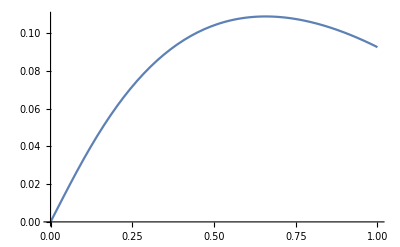

```mathematica
Plot[-(s1 (-2-9 s1+6 s1^2))/(6 (1+2 s1)^2),{s1,0,1}]
```

```mathematica
Factor[Simplify[D[Ep1[s1,s2],s2]/.s2-> s1]]
```

(s1 (2+3 s1))/((1+s1)^2 (1+2 s1)^2)

s2>s1

```mathematica
Ep2[s1_,s2_]:= Integrate[Integrate[beta[t2, s2, s1] + s2(1 - beta[t2, s2, s1 ]) ,{t1,0, t2int[t2, s2, s1]}]+ Integrate[beta[t1, s1, s2] + s1(1 - beta[t1, s1, s2 ]),{t1, t2int[t2, s2, s1], 1}],{t2, 0, 1}]
```

```mathematica
Ep[s1_,s2_]:= If[s1>=s2, Ep1[s1,s2], Ep2[s1,s2]]
```

```mathematica
Plot3D[{Ep[s1,s2]}, {s1, 0, 1}, {s2, 0, 1}, AxesLabel->Automatic]
```

-Graphics3D-

Optimization problem

```mathematica
Minimize[{Ep[s1,s2], Cprize[s1,s2]>= 0.28 && 0<= s1 <= 1 && 0<= s2<= 1},{s1,s2}]
```

{0.840516,{s1→0.878665,s2→0.}}

```mathematica
Cprize[0.890164, 0.078798]
```

0.258818

Final prices

```mathematica
Fp[t1_,t2_,s1_,s2_] := If[beta[t1,s1,s2]>=beta[t2,s2,s1],beta[t1,s1,s2] + s1(1 - beta[t1,s1,s2]),beta[t2,s2,s1] + s2(1 - beta[t2,s2,s1])]
```

```mathematica
Manipulate[Plot3D[{Fp[t1,t2,s1,s2],C},{t1,0,1},{t2,0,1},AxesLabel->Automatic, PlotRange->{0,1}],{s1,0,1},{s2,0,1},{C,0,1}]
```

```mathematica
Manipulate[Plot[{beta[t,s1,s2] + s1(1 - beta[t,s1,s2]),beta[t,s2,s1] + s2(1 - beta[t,s2,s1])},{t,0,1},PlotRange->{0,1}],{s1,0,1},{s2,0,1}]
```

```mathematica
Solve[t2int[t1,s1,s2] == t2int[t1,s1,0],t1]
```

{{t1→(s1/(1+2 s1)-((s1-s2) (1+2 s2))/(s1 (1+s2)+(1+s1) (1+2 s2)))/(-1/(1+2 s1)+(1+2 s2)/(1+2 s1))}}

```mathematica
Manipulate[Plot[{Ep[s1,s2],Ep[s1,0]},{s2,0,1}],{s1,0,1}]
```

```mathematica
Simplify[D[beta[t2,s2,s1],s2]]
```

((1+2 s1) (1+3 s1))/(1+2 s2+s1 (2+3 s2))^2-(2 t2)/(1+2 s2)^2

```mathematica
beta2prima[t2_,s2_,s1_]:= ((1+2 s1) (1+3 s1))/(1+2 s2+s1 (2+3 s2))^2-(2 t2)/(1+2 s2)^2
```

```mathematica
Simplify[(1+((s1-s2) (1+2 s2))/(1+2 s2+s1 (2+3 s2))+(1+2 s2)/(1+2 s1)t1)/(1+2 s2)^2]
```

(1+((s1-s2) (1+2 s2))/(1+2 s2+s1 (2+3 s2))+(t1+2 s2 t1)/(1+2 s1))/(1+2 s2)^2

```mathematica
Simplify[Factor[(1+((s1-s2) (1+2 s2))/(1+2 s2+s1 (2+3 s2)))/(1+2 s2)^2]]
```

(1+s2-2 s2^2+s1 (3+5 s2))/((1+2 s2)^2 (1+2 s2+s1 (2+3 s2)))

```mathematica
Simplify[(-1+2 s1-4 s2)(1+2 s1+2 s2+3 s1 s2)]
```

(-1+2 s1-4 s2) (1+2 s2+s1 (2+3 s2))

```mathematica
Simplify[-1-2 s1+s1^2-4 s2-8 s1 s2-4 s2^2-6 s1 s2^2]
```

s1^2-(1+2 s2)^2-2 s1 (1+4 s2+3 s2^2)

```mathematica
Simplify[Integrate[D[beta[t1,s1,s2],s1],{t1,t2int[t1,s1,s2],1}]]
```

(-2 (1/2-1/2 (1+2 s2)^2 ((s1-s2)/(1+2 s1+2 s2+3 s1 s2)+t1/(1+2 s1))^2)+((1+2 s1) (1+2 s2) (1+3 s2) (2 s1^2 (1+s2)+s1 (3+s2^2 (4-6 t1)-7 s2 (-1+t1)-2 t1)-(1+2 s2) (-1+t1+s2 (-1+2 t1))))/(1+2 s2+s1 (2+3 s2))^3)/(1+2 s1)^2

```mathematica
DifB11[t1_,s1_,s2_]:= (-2 (1/2-1/2 (1+2 s2)^2 ((s1-s2)/(1+2 s1+2 s2+3 s1 s2)+t1/(1+2 s1))^2)+((1+2 s1) (1+2 s2) (1+3 s2) (2 s1^2 (1+s2)+s1 (3+s2^2 (4-6 t1)-7 s2 (-1+t1)-2 t1)-(1+2 s2) (-1+t1+s2 (-1+2 t1))))/(1+2 s2+s1 (2+3 s2))^3)/(1+2 s1)^2
```

```mathematica
Manipulate[Plot3D[DifB11[t1,s1,s2],{s1,0,1},{s2,0,1},AxesLabel->Automatic,PlotRange->All],{t1,0,1}]
```

```mathematica
Plot3D[Integrate[DifB11[t1,s1,s2],{t1,0,1}],{s1,0,1},{s2,0,1},AxesLabel->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
Et1[s1_,s2_]:= Integrate[Integrate[t2 ,{t2,0, t2int[t1, s1, s2]}]+ Integrate[t1,{t2, t2int[t1, s1, s2], 1}],{t1, 0, 1}]
```

```mathematica
Et2[s1_,s2_]:= Integrate[Integrate[t1 ,{t1,0, t2int[t2, s2, s1]}]+ Integrate[t2,{t1, t2int[t2, s2, s1], 1}],{t2, 0, 1}]
```

```mathematica
Et[s1_,s2_]:= If[s1>=s2, Et1[s1,s2], Et2[s1,s2]]
```

```mathematica
Plot3D[Et[s1,s2],{s1,0,1},{s2,0,1},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Manipulate[Plot[{t2int[t1,s1,s2](beta[t1,s1,s2](1-s1) + s1)+ (1 - t2int[t1,s1,s2])((beta[1,s2,s1] + beta[t1,s1,s2])(1- s2)/2 + s2),t2int[t1,s1,0](beta[t1,s1,0](1-s1) + s1)+ (1 - t2int[t1,s1,0])((beta[1,0,s1] + beta[t1,s1,0])/2 )},{t1,0,1},PlotRange->{0,1}],{s1,0,1},{s2,0,1}]
```

```mathematica
Factor[Simplify[D[t2int[t1,s1,s2](beta[t1,s1,s2](1-s1) + s1)+ (1 - t2int[t1,s1,s2])((beta[1,s2,s1] + beta[t1,s1,s2])(1- s2)/2 + s2),t1]]]
```

-((1+2 s2) (-2 s1-4 s1^2+2 s2+2 s1 s2-4 s1^2 s2+2 s2^2+4 s1 s2^2-t1+4 s1^2 t1-3 s2 t1-s1 s2 t1+6 s1^2 s2 t1-2 s2^2 t1-3 s1 s2^2 t1))/((1+2 s1)^2 (1+2 s1+2 s2+3 s1 s2))

```mathematica
Expectedpricegivent1[t1_,s1_,s2_]:=t2int[t1,s1,s2](beta[t1,s1,s2](1-s1) + s1)+ (1 - t2int[t1,s1,s2])((beta[1,s2,s1] + beta[t1,s1,s2])(1- s2)/2 + s2)
```

```mathematica
Simplify[Expectedpricegivent1[0,s1,s2]]
```

(2 s1^3 (1+2 s2)^2+(1+2 s2)^2 (1+3 s2+5 s2^2+3 s2^3)+s1^2 (7+39 s2+75 s2^2+47 s2^3)+s1 (4+22 s2+42 s2^2+26 s2^3-4 s2^4))/(2 (1+2 s2) (1+2 s2+s1 (2+3 s2))^2)

Second attempt

```mathematica
D[t2int[t1,s1,s2],s2]
```

-((s1+2 (1+s1)) (s1-s2) (1+2 s2))/(s1 (1+s2)+(1+s1) (1+2 s2))^2+(2 (s1-s2))/(s1 (1+s2)+(1+s1) (1+2 s2))-(1+2 s2)/(s1 (1+s2)+(1+s1) (1+2 s2))+(2 t1)/(1+2 s1)

```mathematica
phi2diff[t1_,s1_,s2_]:= -((s1+2 (1+s1)) (s1-s2) (1+2 s2))/(s1 (1+s2)+(1+s1) (1+2 s2))^2+(2 (s1-s2))/(s1 (1+s2)+(1+s1) (1+2 s2))-(1+2 s2)/(s1 (1+s2)+(1+s1) (1+2 s2))+(2 t1)/(1+2 s1)
```

```mathematica
D[beta[t1,s1,s2],s2]
```

(1-((s1+2 (1+s1)) (s1-s2) (1+2 s2))/(s1 (1+s2)+(1+s1) (1+2 s2))^2+(2 (s1-s2))/(s1 (1+s2)+(1+s1) (1+2 s2))-(1+2 s2)/(s1 (1+s2)+(1+s1) (1+2 s2)))/(1+s2)-(s2+((s1-s2) (1+2 s2))/(s1 (1+s2)+(1+s1) (1+2 s2)))/(1+s2)^2

```mathematica
beta1diff[s1_,s2_]:= (1-((s1+2 (1+s1)) (s1-s2) (1+2 s2))/(s1 (1+s2)+(1+s1) (1+2 s2))^2+(2 (s1-s2))/(s1 (1+s2)+(1+s1) (1+2 s2))-(1+2 s2)/(s1 (1+s2)+(1+s1) (1+2 s2)))/(1+s2)-(s2+((s1-s2) (1+2 s2))/(s1 (1+s2)+(1+s1) (1+2 s2)))/(1+s2)^2
```

```mathematica
D[beta[t2,s2,s1],s2]
```

(-((1+2 s1) (2+3 s1) (-s1+s2))/((1+s1) s2+(1+2 s1) (1+s2))^2+(1+2 s1)/((1+s1) s2+(1+2 s1) (1+s2)))/(1+s1)-(2 t2)/(1+2 s2)^2

```mathematica
beta2diff[t2_,s2_,s1_]:= (-((1+2 s1) (2+3 s1) (-s1+s2))/((1+s1) s2+(1+2 s1) (1+s2))^2+(1+2 s1)/((1+s1) s2+(1+2 s1) (1+s2)))/(1+s1)-(2 t2)/(1+2 s2)^2
```

```mathematica
beta2diff[t2,0,0]
```

1-2 t2

Boundary Effect

```mathematica
Effboundary[s1_,s2_]:= Integrate[(s1-s2)(1 - beta[t1,s1,s2])phi2diff[t1,s1,s2],{t1,0,1}]
```

Strategic Effect 1

```mathematica
Effstatregic1[s1_,s2_]:=Integrate[Integrate[beta1diff[s1,s2](1-s1),{t2,0,t2int[t1,s1,s2]}],{t1,0,1}]
```

Strategic Effect 2

```mathematica
Effstatregic2[s1_,s2_]:=Integrate[Integrate[beta2diff[t2,s2,s1](1-s2),{t2,t2int[t1,s1,s2],1}],{t1,0,1}]
```

Direct Effect

```mathematica
Effdirect[s1_,s2_]:= Integrate[Integrate[(1-beta[t2,s2,s1]),{t2,t2int[t1,s1,s2],1}],{t1,0,1}]
```

```mathematica
Effdirect[0,0]
```

1/6

Looking for fucking answers

```mathematica
Manipulate[BarChart[{Effboundary[s1,s2],Effstatregic1[s1,s2],Effstatregic2[s1,s2],Effdirect[s1,s2],Effboundary[s1,s2]+Effstatregic1[s1,s2]+Effstatregic2[s1,s2]+Effdirect[s1,s2]},ChartLabels->{"Bound","Strat 1","Strat 2", "Direct","Total"}],{s1,0,1},{s2,0,1}]
```

Stochastic dominance Final price w

```mathematica
Manipulate[Plot[{s1 + (1-s1)beta[t,s1,s2],s2+(1-s2)beta[t,s2,s1]},{t,0,1},PlotRange->{0,1}],{s1,0,1},{s2,0,1}]
```

Dirty effects of the boundary

```mathematica
D[(1+2s2)/(1+2s1),s2]
```

2/(1+2 s1)

```mathematica
Effboundarypos[s1_,s2_]:= Integrate[(s1-s2)(1 - beta[t1,s1,s2])(2t1)/(1+2 s1),{t1,0,1}]
```

```mathematica
Effboundarypos[0.3,0.1]
```

0.047123

```mathematica
Simplify[D[psi[s2,s1],s2]/.s2->0]
```

(-1-2 s1+s1^2)/(1+2 s1)^2

```mathematica
Effboundaryneg[s1_,s2_]:= Integrate[(s1-s2)(1 - beta[t1,s1,s2])(s1^2-(1+2 s2)^2-2 s1 (1+4 s2+3 s2^2))/(1+2 s2+s1 (2+3 s2))^2,{t1,0,1}]
```

```mathematica
Effboundaryneg[0.3,0.2]
```

-0.0297162

Dirty effects of the strategy 2

```mathematica
Simplify[D[(s2+3 s1 s2)/(1+2 s1+2 s2+3 s1 s2),s2]]
```

(1+5 s1+6 s1^2)/(1+2 s2+s1 (2+3 s2))^2

```mathematica
Effstatregic2pos[s1_,s2_]:=Integrate[Integrate[(1-s2)(1+5 s1+6 s1^2)/(1+2 s2+s1 (2+3 s2))^2,{t2,t2int[t1,s1,s2],1}],{t1,0,1}]
```

```mathematica
Simplify[D[beta[t2,s2,s1],s2]]
```

((1+2 s1) (1+3 s1))/(1+2 s2+s1 (2+3 s2))^2-(2 t2)/(1+2 s2)^2

```mathematica
Effstatregic2neg[s1_,s2_]:=Integrate[Integrate[-(1-s2)(2 t2)/(1+2 s2)^2,{t2,t2int[t1,s1,s2],1}],{t1,0,1}]
```

New Bar graph

```mathematica
Manipulate[BarChart[{Effboundarypos[s1,s2],Effboundaryneg[s1,s2],Effstatregic1[s1,s2],Effstatregic2pos[s1,s2],Effstatregic2neg[s1,s2],Effdirect[s1,s2],Effboundary[s1,s2]+Effstatregic1[s1,s2]+Effstatregic2[s1,s2]+Effdirect[s1,s2]},ChartLabels->{"Bound+","Bound-","Strat 1","Strat 2+","Strat 2-", "Direct","Total"}],{s1,0,1},{s2,0,1}]
```